# The Meson nonet from group theory

## Defining the representations

```mathematica
QuarkNames={"s", "d", "u"}
AntiQuarkNames=Table[ToString[OverBar[str], TraditionalForm], {str, QuarkNames}]
```

{s,d,u}

{s̄,d̄,ū}

```mathematica
Quark=1/2*Join[Table[BlockDiagonalMatrix[{PauliMatrix[i], DiagonalMatrix[{0}]}]//Normal, {i, 1, 3}],  {{{0,0,1}, {0,0,0}, {1,0,0}}, {{0,0,-I}, {0,0,0}, {I,0,0}}},  Table[BlockDiagonalMatrix[{{{0}}, PauliMatrix[i]}]//Normal, {i,2}], {1/Sqrt[3] DiagonalMatrix[{1,1,-2}]}];
Table[i//MatrixForm, {i, Quark}]
```

{(0 | 1/2 | 0
1/2 | 0 | 0
0 | 0 | 0),(0 | -ⅈ/2 | 0
ⅈ/2 | 0 | 0
0 | 0 | 0),(1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0),(0 | 0 | 1/2
0 | 0 | 0
1/2 | 0 | 0),(0 | 0 | -ⅈ/2
0 | 0 | 0
ⅈ/2 | 0 | 0),(0 | 0 | 0
0 | 0 | 1/2
0 | 1/2 | 0),(0 | 0 | 0
0 | 0 | -ⅈ/2
0 | ⅈ/2 | 0),(1/(2 √3) | 0 | 0
0 | 1/(2 √3) | 0
0 | 0 | -1/(√3))}

```mathematica
AntiQuark=-1/2 Conjugate[Join[Table[BlockDiagonalMatrix[{PauliMatrix[i], DiagonalMatrix[{0}]}]//Normal, {i, 1, 3}],  {{{0,0,1}, {0,0,0}, {1,0,0}}, {{0,0,-I}, {0,0,0}, {I,0,0}}},  Table[BlockDiagonalMatrix[{{{0}}, PauliMatrix[i]}]//Normal, {i,2}], {1/Sqrt[3] DiagonalMatrix[{1,1,-2}]}]];
Table[i//MatrixForm, {i,AntiQuark}]
```

{(0 | -1/2 | 0
-1/2 | 0 | 0
0 | 0 | 0),(0 | -ⅈ/2 | 0
ⅈ/2 | 0 | 0
0 | 0 | 0),(-1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 0),(0 | 0 | -1/2
0 | 0 | 0
-1/2 | 0 | 0),(0 | 0 | -ⅈ/2
0 | 0 | 0
ⅈ/2 | 0 | 0),(0 | 0 | 0
0 | 0 | -1/2
0 | -1/2 | 0),(0 | 0 | 0
0 | 0 | -ⅈ/2
0 | ⅈ/2 | 0),(-1/(2 √3) | 0 | 0
0 | -1/(2 √3) | 0
0 | 0 | 1/(√3))}

## Casimir Operators

```mathematica
d[i_,j_,k_]:=2Tr[(Quark[[i]].Quark[[j]]+Quark[[j]].Quark[[i]]).Quark[[k]]]
```

```mathematica
f[i_,j_,k_]:=-2ITr[(Quark[[i]].Quark[[j]]-Quark[[j]].Quark[[i]]).Quark[[k]]]
```

```mathematica
Sum[i.i, {i, Quark}]
```

(4/3 | 0 | 0
0 | 4/3 | 0
0 | 0 | 4/3)

```mathematica
Sum[d[i,j,k]*Quark[[i]].Quark[[j]].Quark[[k]], {i, 8}, {j, 8}, {k, 8}]
```

(10/9 | 0 | 0
0 | 10/9 | 0
0 | 0 | 10/9)

## Product Representation - Mesons

```mathematica
QxAQ=Table[KroneckerProduct[Quark[[i]], IdentityMatrix[3]]+KroneckerProduct[IdentityMatrix[3],AntiQuark[[i]] ], {i, 8}];
Table[mat//MatrixForm, {mat, QxAQ}];
```

```mathematica
Cas1=Sum[mat.mat, {mat,QxAQ}]
```

(2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1
0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
-1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2)

```mathematica
Eigenvalues[Cas1]
```

{3,3,3,3,3,3,3,3,0}

```mathematica
U=Table[row//Normalize, {row, Eigenvectors[Cas1]}]
```

(-1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√3) | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 1/(√3))

```mathematica
Cas2=Sum[d[i,j,k]*QxAQ[[i]].QxAQ[[j]].QxAQ[[k]], {i, 8}, {j, 8}, {k, 8}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[Cas2]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
Ualt=Table[row//Normalize, {row, Eigenvectors[Cas2]}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
U-Ualt
```

(-1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2)-1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√2) | 0 | 0 | 0 | 1/(√2)-1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√3)-1 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 1/(√3))

```mathematica
MesonNonet=Table[(U.mat.Inverse[U]//FullSimplify)//MatrixForm, {mat, QxAQ}]
```

{(0 | 0 | 0 | 0 | 0 | -1/(2 √2) | 0 | 1/(2 √2) | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | ⅈ/(2 √2) | 0 | ⅈ/(2 √2) | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | ⅈ/(√2) | 0
0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
-1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | -1/(2 √2) | 0 | 0 | 0 | 1/(2 √2) | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
-ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | ⅈ/(2 √2) | 0 | 0 | 0 | ⅈ/(2 √2) | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
-ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | -1/(2 √2) | 0 | 1/(2 √2) | 0 | 0 | 0 | 0 | 0
-1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0
0 | 1/(2 √2) | 0 | -1/(2 √2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | ⅈ/(2 √2) | 0 | ⅈ/(2 √2) | 0 | 0 | 0 | 0 | 0
-ⅈ/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
-ⅈ/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0
0 | -ⅈ/(2 √2) | 0 | -ⅈ/(2 √2) | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
U.Cas1.Inverse[U]//FullSimplify
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Cols=Table[StringJoin[i,j], {i, QuarkNames}, {j, AntiQuarkNames}]//Flatten
```

{ss̄,sd̄,sū,ds̄,dd̄,dū,us̄,ud̄,uū}

```mathematica
MesonNames=U.Cols
```

{(uū)/(√2)-(ss̄)/(√2),ud̄,us̄,dū,(dd̄)/(√2)-(ss̄)/(√2),ds̄,sū,sd̄,(dd̄)/(√3)+(ss̄)/(√3)+(uū)/(√3)}

```mathematica
I3=Diagonal[MesonNonet[[3]]//First//Normal]
```

{0,1/2,-1/2,-1/2,0,-1,1/2,1,0}

```mathematica
Q=-2/Sqrt[3]*Diagonal[MesonNonet[[8]]//First//Normal]
```

{0,1,1,-1,0,0,-1,0,0}

```mathematica
TableForm[{I3, Q}, TableAlignments->Center, TableHeadings->{{ "I_3", "Q"},MesonNames}]
```

| -(ss̄)/(√2)+(uū)/(√2) | ud̄ | us̄ | dū | (dd̄)/(√2)-(ss̄)/(√2) | ds̄ | sū | sd̄ | (dd̄)/(√3)+(ss̄)/(√3)+(uū)/(√3)
I_3 | 0 | 1/2 | -1/2 | -1/2 | 0 | -1 | 1/2 | 1 | 0
Q | 0 | 1 | 1 | -1 | 0 | 0 | -1 | 0 | 0

## Product Representation - Baryons

```mathematica
QxQxQ=Table[KroneckerProduct[Quark[[i]], IdentityMatrix[3], IdentityMatrix[3]]+KroneckerProduct[IdentityMatrix[3], Quark[[i]],  IdentityMatrix[3]]+KroneckerProduct[IdentityMatrix[3],IdentityMatrix[3], Quark[[i]] ], {i, 8}];
Table[mat//MatrixForm, {mat, QxQxQ}];
```

```mathematica
Cas1B=Sum[mat.mat, {mat,QxQxQ}]
```

(6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6)

```mathematica
Eigenvalues[Cas1B]
```

{6,6,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0}

```mathematica
UB=Table[row//Normalize, {row, Eigenvectors[Cas1B]}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 1/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | -1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0)

```mathematica
Cas2B=Sum[d[i,j,k]*QxQxQ[[i]].QxQxQ[[j]].QxQxQ[[k]], {i, 8}, {j, 8}, {k, 8}]
```

(9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0
0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0
0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9)

```mathematica
Eigenvalues[Cas2B]
```

{9,9,9,9,9,9,9,9,9,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
UaltB=Table[row//Normalize, {row, Eigenvectors[Cas2B]}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 1/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
UB-UaltB
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 1/(√2) | 1/(√2) | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√2) | 1/(√2) | 1/(√2) | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | -1/(√2) | 0 | -1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | -1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0)

```mathematica
Baryons=Table[(UB.mat.Inverse[UB]//FullSimplify)//MatrixForm, {mat, QxQxQ}];
```

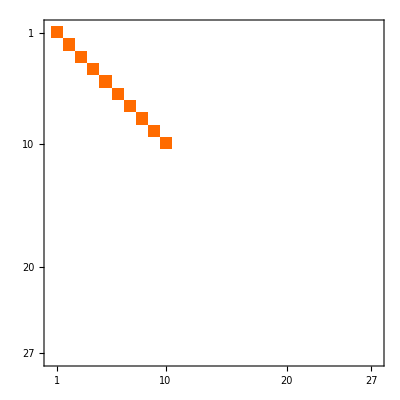

```mathematica
UB.Cas2B.Inverse[UB]//FullSimplify//MatrixPlot
```

```mathematica
Cols=Table[StringJoin[i,j,k], {i, QuarkNames}, {j, QuarkNames}, {k, QuarkNames}]//Flatten
```

{sss,ssd,ssu,sds,sdd,sdu,sus,sud,suu,dss,dsd,dsu,dds,ddd,ddu,dus,dud,duu,uss,usd,usu,uds,udd,udu,uus,uud,uuu}

```mathematica
BaryonNames=UB.Cols;
BaryonNames=Table[ToString[name, TraditionalForm], {name, BaryonNames}];
```

```mathematica
I3B=Diagonal[Baryons[[3]]//First//Normal]
```

{0,-1/2,1/2,-1,0,1,-3/2,-1/2,1/2,3/2,-1/2,1/2,-1/2,-1,0,1/2,0,1,-1,0,-1/2,0,-1/2,1/2,1,1/2,0}

```mathematica
QB=-2/Sqrt[3]*Diagonal[Baryons[[8]]//First//Normal]
```

{2,1,1,0,0,0,-1,-1,-1,-1,1,1,1,0,0,1,0,0,0,0,-1,0,-1,-1,0,-1,0}

```mathematica
TableForm[{I3B, QB}, TableAlignments->Center, TableHeadings->{{ "I_3", "Q"},BaryonNames}]
```

| uuu | duu/(√3)+udu/(√3)+uud/(√3) | suu/(√3)+usu/(√3)+uus/(√3) | ddu/(√3)+dud/(√3)+udd/(√3) | dsu/(√6)+dus/(√6)+sdu/(√6)+sud/(√6)+uds/(√6)+usd/(√6) | ssu/(√3)+sus/(√3)+uss/(√3) | ddd | dds/(√3)+dsd/(√3)+sdd/(√3) | dss/(√3)+sds/(√3)+ssd/(√3) | sss | uud/(√2)-duu/(√2) | uus/(√2)-suu/(√2) | udu/(√2)-duu/(√2) | udd/(√2)-ddu/(√2) | uds/(√2)-sud/(√2) | usu/(√2)-suu/(√2) | usd/(√2)-sdu/(√2) | uss/(√2)-ssu/(√2) | dud/(√2)-ddu/(√2) | dus/(√2)-sdu/(√2) | dds/(√2)-sdd/(√2) | dsu/(√2)-sud/(√2) | dsd/(√2)-sdd/(√2) | dss/(√2)-ssd/(√2) | sus/(√2)-ssu/(√2) | sds/(√2)-ssd/(√2) | dsu/(√6)-dus/(√6)-sdu/(√6)+sud/(√6)+uds/(√6)-usd/(√6)
I_3 | 0 | -1/2 | 1/2 | -1 | 0 | 1 | -3/2 | -1/2 | 1/2 | 3/2 | -1/2 | 1/2 | -1/2 | -1 | 0 | 1/2 | 0 | 1 | -1 | 0 | -1/2 | 0 | -1/2 | 1/2 | 1 | 1/2 | 0
Q | 2 | 1 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | 0

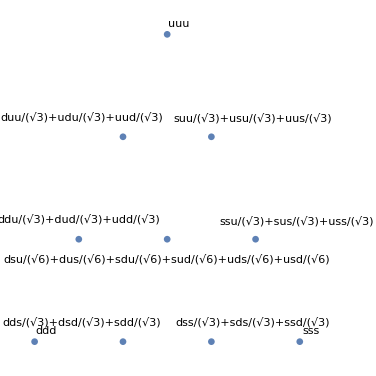

```mathematica
ListPlot[Table[Labeled[{I3B[[i]], QB[[i]]}, BaryonNames[[i]], LabelStyle->Small], {i, 10}], AspectRatio->1, Axes->False]
```

```mathematica
ListPlot[Table[Labeled[{I3B[[i]], QB[[i]]}, BaryonNames[[i]], LabelStyle->Small], {i, 11, 27}], AspectRatio->1, Axes->False]
```

-Graphics-